```mathematica
Clear[x,y]
f[x_,y_]=5*Cos[y]-Sin[x]+x^2;
a=0;b=1;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];x0=0;y0=0.5;
```

```mathematica
(*метод Эйлера Коши*)
```

```mathematica
eulk1=Table[{x0,y0}={x0+h1,y0+h1/2*(f[x0,y0]+f[x0+h1,y0+h1*f[x0,y0]])},{i,0,n1-1}]
```

{{0.1,0.862595},{0.2,1.10828},{0.3,1.26475},{0.4,1.36209},{0.5,1.42287},{0.6,1.46227},{0.7,1.4901},{0.8,1.51262},{0.9,1.53383},{1.,1.55628}}

```mathematica
eulk1//Column
```

{0.1,0.862595}
{0.2,1.10828}
{0.3,1.26475}
{0.4,1.36209}
{0.5,1.42287}
{0.6,1.46227}
{0.7,1.4901}
{0.8,1.51262}
{0.9,1.53383}
{1.,1.55628}

```mathematica
eulk1=Prepend[eulk1,{0,0}]
```

{{0,0},{0.1,0.862595},{0.2,1.10828},{0.3,1.26475},{0.4,1.36209},{0.5,1.42287},{0.6,1.46227},{0.7,1.4901},{0.8,1.51262},{0.9,1.53383},{1.,1.55628}}

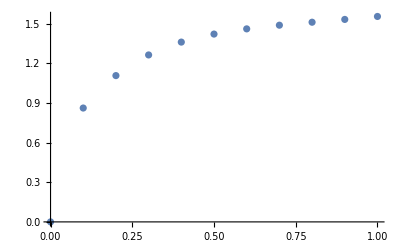

```mathematica
gr1=ListPlot[eulk1]
```

```mathematica
x0=0;y0=0.5;
eulk2=Table[{x0,y0}={x0+h2,y0+h2/2*(f[x0,y0]+f[x0+h2,y0+h2*f[x0,y0]])},{i,0,n2-1}]
```

{{0.05,0.702536},{0.1,0.873087},{0.15,1.01241},{0.2,1.12387},{0.25,1.21179},{0.3,1.28054},{0.35,1.33404},{0.4,1.37562},{0.45,1.408},{0.5,1.4334},{0.55,1.45358},{0.6,1.46993},{0.65,1.48356},{0.7,1.49534},{0.75,1.50597},{0.8,1.51597},{0.85,1.52579},{0.9,1.53576},{0.95,1.54615},{1.,1.55718}}

```mathematica
eulk2=Prepend[eulk2,{0,0}]
```

{{0,0},{0.05,0.702536},{0.1,0.873087},{0.15,1.01241},{0.2,1.12387},{0.25,1.21179},{0.3,1.28054},{0.35,1.33404},{0.4,1.37562},{0.45,1.408},{0.5,1.4334},{0.55,1.45358},{0.6,1.46993},{0.65,1.48356},{0.7,1.49534},{0.75,1.50597},{0.8,1.51597},{0.85,1.52579},{0.9,1.53576},{0.95,1.54615},{1.,1.55718}}

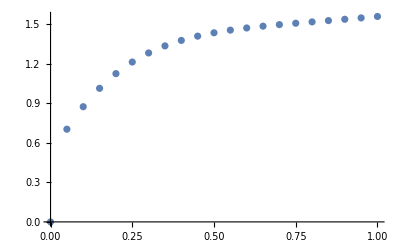

```mathematica
gr2=ListPlot[eulk2]
```

```mathematica
(*б)Метод Рунге-Кутта*)
```

```mathematica
Clear[x,y]
```

```mathematica
f[x_,y_]=5*Cos[y]-Sin[x]+x^2;
a=0;b=1;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];x0=0;y0=0.5;
```

```mathematica
sol1=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<n1+1,k++,
k1[x_,y_]=h1*f[x,y];
k2[x_,y_]=h1*f[x+h1/2,y+k1[x,y]/2];
k3[x_,y_]=h1*f[x+h1/2,y+k2[x,y]/2];
k4[x_,y_]=h1*f[x+h1,y+k3[x,y]];
x=x+h1;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol1=Append[sol1,{x,y}]]
```

```mathematica
sol1
```

{{0,0.5},{0.1,0.875787},{0.2,1.12775},{0.3,1.28438},{0.4,1.37883},{0.5,1.43585},{0.6,1.47166},{0.7,1.49649},{0.8,1.51667},{0.9,1.53613},{1.,1.55731}}

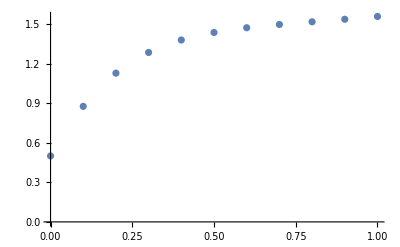

```mathematica
gr3=ListPlot[sol1]
```

```mathematica
Clear[so12]
```

```mathematica
sol2=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n2+1,k++,
k1[x_,y_]=h2*f[x,y];
k2[x_,y_]=h2*f[x+h2/2,y+k1[x,y]/2];
k3[x_,y_]=h2*f[x+h2/2,y+k2[x,y]/2];
k4[x_,y_]=h2*f[x+h2,y+k3[x,y]];
x=x+h2;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol2=Append[sol2,{x,y}]]
```

```mathematica
sol2
```

{{0,0.5},{0.05,0.704104},{0.1,0.875906},{0.15,1.01606},{0.2,1.12795},{0.25,1.21597},{0.3,1.28459},{0.35,1.33781},{0.4,1.37902},{0.45,1.411},{0.5,1.43599},{0.55,1.45578},{0.6,1.47177},{0.65,1.48507},{0.7,1.49657},{0.75,1.50694},{0.8,1.51672},{0.85,1.52635},{0.9,1.53616},{0.95,1.54641},{1.,1.55732}}

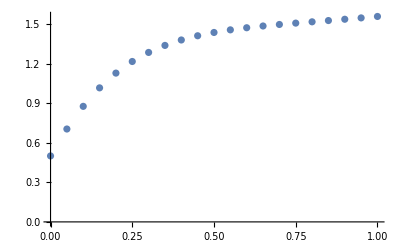

```mathematica
gr4=ListPlot[sol2]
```

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
eqn=y'[x]==5*Cos[y[x]]-Sin[x]+x^2;
initialCondition=y[0]==0.5;
solutionDSolve=DSolve[{eqn,initialCondition},y,x];
y1[x_]=y[x]/.Flatten[solutionDSolve]
Print["Аналитическое решение: ",solutionDSolve];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ReplaceAll::reps: {DSolve[{y'[x]==x^2+5 Cos[y[«1»]]-Sin[x],y[0]==0.5},y,x]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y[x]/.DSolve[{y'[x]==x^2+5 Cos[y[x]]-Sin[x],y[0]==0.5},y,x]

Аналитическое решение: DSolve[{y'[x]==x^2+5 Cos[y[x]]-Sin[x],y[0]==0.5},y,x]

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
eqn=y'[x]==5*Cos[y[x]]-Sin[x]+x^2;
initialCondition=y[0]==0.5;
solutionNDSolve=NDSolve[{eqn,initialCondition},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

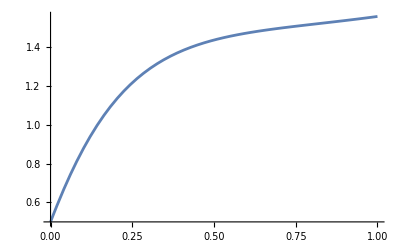

```mathematica
gr5=Plot[Evaluate[y[x]/.solutionNDSolve],{x,0,1}]
```

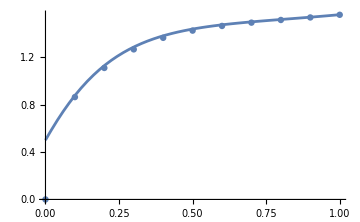

```mathematica
Show[gr1,gr5,ImageSize->Medium]
```

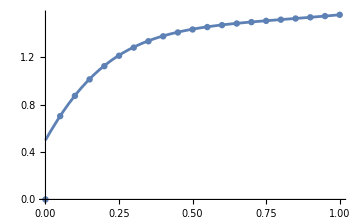

```mathematica
Show[gr2,gr5,ImageSize->Medium]
```

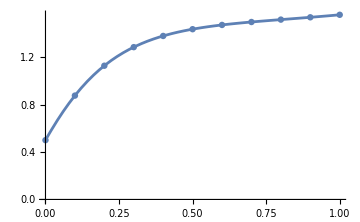

```mathematica
Show[gr3,gr5,ImageSize->Medium]
```

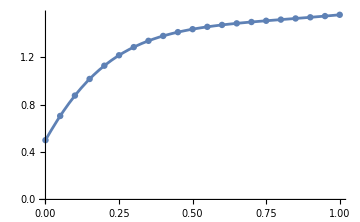

```mathematica
Show[gr4,gr5,ImageSize->Medium]
```